```mathematica
(*********************************************************)
(*                                                         *)
(*   Constructing Hamiltonian                              *)
(*                                                         *)
(*********************************************************)
```

```mathematica
Unit[H_]:=FullSimplify[MatrixExp[-ⅈ*H]]
```

```mathematica
S = {{1,0,0,0},
    {0,0,1,0},
    {0,1,0,0},
    {0,0,0,1}};
eye = {{1,0},{0,1}};
eye2=KroneckerProduct[eye,eye];
```

```mathematica
U = KroneckerProduct[S,eye].KroneckerProduct[eye,S];
U//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
H = FullSimplify[MatrixLog[U]*ⅈ];
H/((2 ⅈ π)/(3 √3))//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Unit[H]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
vec = Eigenvectors[H];
Eigenvalues[H]
val = DiagonalMatrix[Eigenvalues[H]];
ConjugateTranspose[vec]//MatrixForm
```

{-(2 π)/3,-(2 π)/3,(2 π)/3,(2 π)/3,0,0,0,0}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1/2 (-1-ⅈ √3) | 0 | 1/2 (-1+ⅈ √3) | 0 | 0 | 1 | 0
0 | 1/2 (-1+ⅈ √3) | 0 | 1/2 (-1-ⅈ √3) | 0 | 0 | 1 | 0
1/2 (-1+ⅈ √3) | 0 | 1/2 (-1-ⅈ √3) | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1/2 (-1-ⅈ √3) | 0 | 1/2 (-1+ⅈ √3) | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
FullSimplify[ConjugateTranspose[vec].val.vec]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 ⅈ π)/(√3) | 0 | (2 ⅈ π)/(√3) | 0 | 0 | 0
0 | (2 ⅈ π)/(√3) | 0 | 0 | -(2 ⅈ π)/(√3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 ⅈ π)/(√3) | -(2 ⅈ π)/(√3) | 0
0 | -(2 ⅈ π)/(√3) | (2 ⅈ π)/(√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(2 ⅈ π)/(√3) | 0 | 0 | (2 ⅈ π)/(√3) | 0
0 | 0 | 0 | (2 ⅈ π)/(√3) | 0 | -(2 ⅈ π)/(√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
plus = 1/2 (-1-ⅈ √3);
minus = 1/2 (-1+ⅈ √3);
Eplus = 2*Pi/3;
Eminus = -2*Pi/3;
```

```mathematica
cob = {{√3,0,0, 0,         0,         0,         0,         0},
             {0,1,0,0,  plus,         0,minus,         0},
             {0,1,0,0,minus,         0,plus,           0},
             {0,0,1,0,         0,         1,         0,         1},
             {0,1,0,0,         1,         0,         1,         0},
             {0,0,1,0,         0,minus,         0,  plus},
             {0,0,1,0,         0,  plus,         0,minus},
             {0,0,0,√3,     0,         0,         0,         0}}/√3;
ener = DiagonalMatrix[{0,0,0,0,Eplus,Eplus,Eminus,Eminus}];
(*ener = DiagonalMatrix[{0,0,0,0,0,0,0,Eminus}];*)
ener//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (2 π)/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 π)/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(2 π)/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 π)/3)

```mathematica
FullSimplify[cob  . ener. ConjugateTranspose[cob]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 ⅈ π)/(3 √3) | 0 | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0
0 | -(2 ⅈ π)/(3 √3) | 0 | 0 | (2 ⅈ π)/(3 √3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | 0
0 | (2 ⅈ π)/(3 √3) | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 ⅈ π)/(3 √3) | 0 | 0 | -(2 ⅈ π)/(3 √3) | 0
0 | 0 | 0 | -(2 ⅈ π)/(3 √3) | 0 | (2 ⅈ π)/(3 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[Unit[cob  . ener. ConjugateTranspose[cob] t]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 (1+2 Cos[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0 | 0 | 0
0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 1/3 (1+2 Cos[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0 | 0 | 0
0 | 0 | 0 | 1/3 (1+2 Cos[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0
0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0 | 1/3 (1+2 Cos[(2 π t)/3]) | 0 | 0 | 0
0 | 0 | 0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0 | 1/3 (1+2 Cos[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0
0 | 0 | 0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 1/3 (1+2 Cos[(2 π t)/3]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Spin3 = DiagonalMatrix[{0,1,1,2,1,2,2,3}];
Spin3.H - H.Spin3 //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*********************************************************)
(*                                                         *)
(*   Energy States over Time                               *)
(*                                                         *)
(*********************************************************)
```

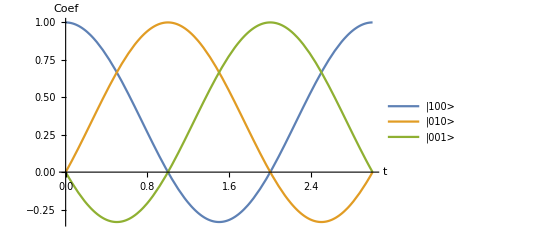

```mathematica
Plot[{
1/3 (1+2 Cos[(2 π t)/3]),
1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]),
1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3])
},{t,0,3},PlotLegends->{"|100>","|010>","|001>"},AxesLabel->{t,"Coef"}]
```

```mathematica
(*********************************************************)
(*                                                         *)
(*   Multi-Spin Single Chain                               *)
(*                                                         *)
(*********************************************************)
```

```mathematica
H5 = KroneckerProduct[H,eye2]+KroneckerProduct[eye2,H];
U5 = Unit[H5];
U5t = Unit[H5 t];
```

```mathematica
ConjugateTranspose[U5t][[5]]
```

{0,1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]]),0,1/5 (1+4 Cos[2/3 √(5/3) π Conjugate[t]]),0,0,0,1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),0,0,0,0,0,0,0,1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

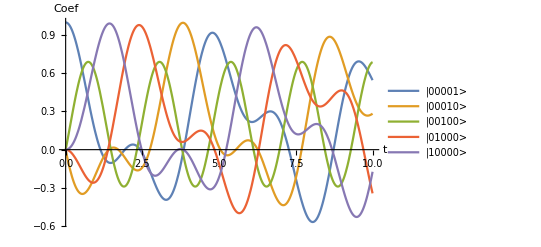

```mathematica
Plot[{
1/10 (2+3 Cos[2/3 √(5/3) π t]+5 Cos[(2 π t)/(3 √3)]),1/10 (2-2 Cos[2/3 √(5/3) π t]-√5 Sin[2/3 √(5/3) π t]-5 Sin[(2 π t)/(3 √3)]),1/5 (1-Cos[2/3 √(5/3) π t]+√5 Sin[2/3 √(5/3) π t]),
1/10 (2+3 Cos[2/3 √(5/3) π t]-5 Cos[(2 π t)/(3 √3)]),1/10 (2-2 Cos[2/3 √(5/3) π t]-√5 Sin[2/3 √(5/3) π t]+5 Sin[(2 π t)/(3 √3)])
},{t,0,10},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},AxesLabel->{t,"Coef"}]
```

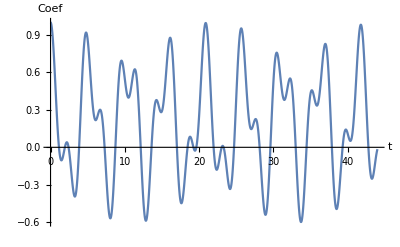

```mathematica
Plot[{1/10 (2+3 Cos[2/3 √(5/3) π t]+5 Cos[(2 π t)/(3 √3)])},{t,0,44},AxesLabel->{t,"Coef"}]
```

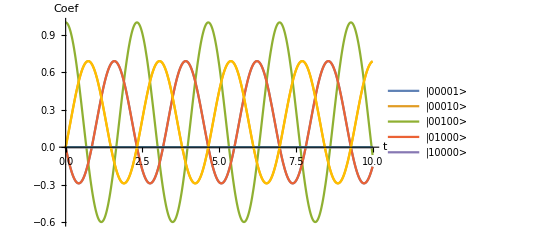

```mathematica
Plot[{
1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]]),1/5 (1+4 Cos[2/3 √(5/3) π Conjugate[t]]),1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),0,0,0,1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]])},{t,0,10},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},AxesLabel->{t,"Coef"}]
```

```mathematica
(*********************************************************)
(*                                                         *)
(*   Multi-Spin Full Chain                                 *)
(*                                                         *)
(*********************************************************)
```

```mathematica
H52 = KroneckerProduct[H,eye2]+KroneckerProduct[eye2,H]+KroneckerProduct[eye,KroneckerProduct[H,eye]];
U52 = Unit[H52];
U52t = Unit[H52 t];
```

$Aborted

$Aborted

```mathematica
ConjugateTranspose[U52t][[5]]
```

```mathematica
Plot[{

},{t,0,10},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},AxesLabel->{t,"Coef"}]
```

```mathematica
{{0, 1/3 (1+2 Cos[(2 π t)/3]), 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]), 0, 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]), 0, 0, 0}}
```